```mathematica
CalculateVectorLength[v_] := FullSimplify[Sqrt[v.v]]
CalculateTangentVector[curve_][t_] := Module[{ A=D[curve[tt],tt]}, FullSimplify[A / CalculateVectorLength[A]]] /. tt -> t
CalculateBinormalVector[curve_][t_] := Module[{ A=Cross[D[curve[tt], tt], D[curve[tt], { tt, 2 }]] }, FullSimplify[A / CalculateVectorLength[A]]] /. tt->t
RotateVectorInPlane[{p1_,p2_}]:={-p2,p1}
RotateVectorInPlane[{ p1_, p2_,p3_}] := { -p2, p1,p3 }
CalculateNormalVector[curve_][t_] := RotateVectorInPlane[CalculateTangentVector[curve][t]]
a=4;
```

```mathematica
c1[t_] := { t, a*Cosh[t/a]}
Print["T = ", CalculateTangentVector[c1][t]]
Print["N = ", CalculateNormalVector[c1][t]]
```

T = {1/(√(Cosh[t/4]^2)),Sinh[t/4]/(√(Cosh[t/4]^2))}

N = {-Sinh[t/4]/(√(Cosh[t/4]^2)),1/(√(Cosh[t/4]^2))}

```mathematica
CalculatePlaneCurvature[curve_][t_] := Module[{ A = D[curve[tt],{tt, 2}], B = D[curve[tt], tt]}, FullSimplify[A . RotateVectorInPlane[B] / CalculateVectorLength[B]^3]] /. tt -> t
Print["K = ", CalculatePlaneCurvature[c1][t]]
```

K = Cosh[t/4]/(4 (Cosh[t/4]^2)^(3/2))

```mathematica
CalculateEvolute[curve_][t_] := FullSimplify[curve[t] + (CalculateNormalVector[curve][t] / CalculatePlaneCurvature[curve][t])]
Evolute = CalculateEvolute[c1][t];
Print["Evolute = ", Evolute]
```

Evolute = {t-2 Sinh[t/2],8 Cosh[t/4]}

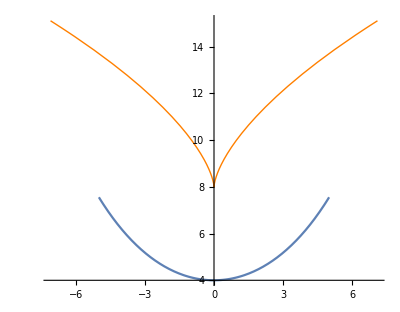

```mathematica
Curve1Plot = ParametricPlot[c1[t], {t,-5,5}];
Evolute1Plot = ParametricPlot[Evolute, {t,-5,5}, PlotStyle-> {Thick,Orange}];
Show[Curve1Plot, Evolute1Plot, PlotRange->All,AspectRatio->Full]
```

```mathematica
GenerateVectorGraphics[curve_][t_] := Graphics[{
	PointSize[0.02], Point[curve[t]],
	Thick,Blue,Arrow[{curve[t], curve[t]+CalculateTangentVector[curve][t]}],
	Thick,Red,Arrow[{curve[t],curve[t]+CalculateNormalVector[curve][t]}]}];
Animate[Show[Curve1Plot, GenerateVectorGraphics[c1][t],AspectRatio->Automatic],{t,-5,5}]
```

```mathematica
c2[t_]:={Cos[t],Sin[t],-a*t}/Sqrt[1+a^2t^2]
Curve2Plot=ParametricPlot3D[c2[t],{t,-5,5},AxesLabel->{"x", "y", "z"},PlotRange->All]
```

-Graphics3D-

```mathematica
CalculateTangentLine[curve_][length_, t_]:=FullSimplify[Line[{curve[tt],curve[tt]+length*CalculateTangentVector[curve][tt]}]]/.tt->t
CalculateNormalLine[curve_][length_,t_]:=FullSimplify[Line[{curve[tt],curve[tt]+length*CalculateNormalVector[curve][tt]}]]/.tt->t
```

```mathematica
Print["Tangent Line = ", CalculateTangentLine[c2][len,t]]
Print["Normal Line = ", CalculateNormalLine[c2][len,t]]
```

Tangent Line = Line[{{Cos[t]/(√(1+16 t^2)),Sin[t]/(√(1+16 t^2)),-(4 t)/(√(1+16 t^2))},{((1+16 t^2) Cos[t]-(len (Sin[t]+16 t (Cos[t]+t Sin[t])))/(√((17+16 t^2)/((1+16 t^2)^2))))/((1+16 t^2)^(3/2)),((1+16 t^2) Sin[t]+(len (Cos[t]+16 t^2 Cos[t]-16 t Sin[t]))/(√((17+16 t^2)/((1+16 t^2)^2))))/((1+16 t^2)^(3/2)),(4 (-t-16 t^3-len/(√((17+16 t^2)/((1+16 t^2)^2)))))/((1+16 t^2)^(3/2))}}]

Normal Line = Line[{{Cos[t]/(√(1+16 t^2)),Sin[t]/(√(1+16 t^2)),-(4 t)/(√(1+16 t^2))},{((1+16 t^2) Cos[t]-(len (Cos[t]+16 t^2 Cos[t]-16 t Sin[t]))/(√((17+16 t^2)/((1+16 t^2)^2))))/((1+16 t^2)^(3/2)),((1+16 t^2) Sin[t]-(len (Sin[t]+16 t (Cos[t]+t Sin[t])))/(√((17+16 t^2)/((1+16 t^2)^2))))/((1+16 t^2)^(3/2)),(4 (-t-16 t^3-len/(√((17+16 t^2)/((1+16 t^2)^2)))))/((1+16 t^2)^(3/2))}}]

```mathematica
Curve2Point={1,0,0};
Reduce[c2[t]==Curve2Point, t]
Print["Tangent Line through P(1, 0, 0) with length 1 = ", CalculateTangentLine[c2][1, 0]]
Print["Normal Line through P(1, 0, 0) with length 1 = ", CalculateNormalLine[c2][1,0]]

Curve2PointGraphic=Graphics3D[{PointSize[0.02], Point[{1,0,0}]}];
Show[Curve2Plot,Curve2PointGraphic, Graphics3D[{Thick, Blue, CalculateTangentLine[c2][3,0], Thick, Red, CalculateNormalLine[c2][3,0]}]]
```

t==0

Tangent Line through P(1, 0, 0) with length 1 = Line[{{1,0,0},{1,1/(√17),-4/(√17)}}]

Normal Line through P(1, 0, 0) with length 1 = Line[{{1,0,0},{1-1/(√17),0,-4/(√17)}}]

-Graphics3D-

```mathematica
CalculateOsculatingPlane[curve_][x_, y_][t_]:=Module[{V=CalculateBinormalVector[curve][tt], P=curve[tt]}, FullSimplify[(V.P-V[[1]]*x-V[[2]]*y)/V[[3]]]] /.tt->t
CalculateRectifyingPlane[curve_][x_,y_][t_]:=Module[{V=CalculateNormalVector[curve][tt],P=curve[tt]},FullSimplify[(V.P-V[[1]]*x-V[[2]]*y)/V[[3]]]]/.tt->t
Print["Z of the Osulating Plane = ", CalculateOsculatingPlane[c2][x,y][t]]
Print["Z of the Rectifying Plane = ", CalculateRectifyingPlane[c2][x,y][t]]
```

Z of the Osulating Plane = (-4 t (1+16 t^2)^(3/2)-4 (17 y+16 t (x+t y)) Cos[t]+(68 x+64 t^2 x-64 t y) Sin[t])/(17+32 (t^2+8 t^4))

Z of the Rectifying Plane = (1+16 (-1+t) t-√(1+16 t^2) ((x+16 t^2 x+16 t y) Cos[t]+(y+16 t (-x+t y)) Sin[t]))/(4 √(1+16 t^2))

```mathematica
Curve2OsculatingPlanePlot=Module[{F=CalculateOsculatingPlane[c2][x,y][0]}, Plot3D[F,{x,-1.5,1.5},{y,-1.5,1.5}]];
Curve2RectifyingPlanePlot=Module[{F=CalculateRectifyingPlane[c2][x,y][0]},Plot3D[F,{x,-1.5,1.5},{y,-1.5,1.5}]];
Show[Curve2Plot,Curve2PointGraphic,Curve2OsculatingPlanePlot,Curve2RectifyingPlanePlot]
```

-Graphics3D-

```mathematica
Rotate2DCurveAroundZ[curve_][u_,v_]:=Module[{V=curve[uu]},FullSimplify[{Cos[vv]*V[[1]],Sin[vv]*V[[1]],V[[2]]}]]/.{uu->u,vv->v}
RotateCurve1AroundZ[u_,v_]:=Rotate2DCurveAroundZ[c1][u,v]
Curve1SurfaceOfRevolution=RotateCurve1AroundZ[u,v];
Print["Surface of revolution: ", Curve1SurfaceOfRevolution]

ParametricPlot3D[Curve1SurfaceOfRevolution,{u,-2,2},{v,0,Pi},AxesLabel->{"x", "y", "z"}]
```

Surface of revolution: {u Cos[v],u Sin[v],4 Cosh[u/4]}

-Graphics3D-

```mathematica
CalculateFirstFundamentalForm[surface_][u_,v_]:=Module[{DU=D[surface[uu,vv],uu],DV=D[surface[uu,vv],vv]},FullSimplify[{DU.DU,DU.DV,DV.DV}]]/.{uu->u,vv->v}
CalculateSecondFundamentalForm[surface_][u_,v_]:=Module[{FDC=Cross[D[surface[uu,vv],uu],D[surface[uu,vv],vv]]},l=FDC/CalculateVectorLength[FDC];FullSimplify[{l.D[surface[uu,vv],{uu,2}],l.D[surface[uu,vv],uu,vv],l.D[surface[uu,vv],{vv,2}]}]]/.{uu->u,vv->v}
CalculateGaussCurvature[fff_,sff_]:=FullSimplify[(sff[[1]]*sff[[3]]-sff[[2]]^2)/(fff[[1]]*fff[[3]]-fff[[2]]^2)]
CalculateMeanCurvature[fff_,sff_]:=FullSimplify[(fff[[1]]*sff[[3]]+fff[[3]]*sff[[1]]-2*fff[[2]]*sff[[2]])/(2*(fff[[1]]*fff[[3]]-fff[[2]]^2))]

Module[{FFF=CalculateFirstFundamentalForm[RotateCurve1AroundZ][u,v],SFF=CalculateSecondFundamentalForm[RotateCurve1AroundZ][u,v]},Print["E = ",FFF[[1]],", F = ",FFF[[2]],", G = ",FFF[[3]]];Print["L = ",SFF[[1]],", M = ",SFF[[2]],", N = ",SFF[[3]]];
Print["K = ",CalculateGaussCurvature[FFF,SFF]];
Print["H = ",CalculateMeanCurvature[FFF,SFF]]]
```

E = Cosh[u/4]^2, F = 0, G = u^2

L = (u Cosh[u/4])/(4 √(u^2 Cosh[u/4]^2)), M = 0, N = (u^2 Sinh[u/4])/(√(u^2 Cosh[u/4]^2))

K = (Sech[u/4]^2 Tanh[u/4])/(4 u)

H = (Sech[u/4] (u+2 Sinh[u/2]))/(8 √(u^2 Cosh[u/4]^2))

```mathematica
Curve2RotationAxis={1,a,1};
Curve2RotationTransform=RotationTransform[a*Pi/6, Curve2RotationAxis]
Show[Curve2Plot,Graphics3D[{Thick,Green,Line[{-Curve2RotationAxis,Curve2RotationAxis}]}],ParametricPlot3D[Curve2RotationTransform[c2[t]],{t,-5,5},PlotStyle->Orange]]
```

TransformationFunction[(-5/12 | 1/12 (4-√6) | 1/12 (1+4 √6) | 0
1/12 (4+√6) | 5/6 | 1/12 (4-√6) | 0
1/12 (1-4 √6) | 1/12 (4+√6) | -5/12 | 0
0 | 0 | 0 | 1)]

-Graphics3D-